## Notebook Programming Environment

A notebook can be  treated as a scratch pad. Mix graphs, text and code.
Notebooks can contain dynamic objects to create a GUI

Editing in a notebook

Try in plain english.

solve the recursive equation a[n] =

```mathematica
a[n] == a[n - 2] + a[n - 1]
```

a[n]==a[-2+n]+a[-1+n]

Autocomplete

```mathematica
Plot3D[
```

Spell checker command ;

Suggestion Bar

```mathematica
Fibonacci[100]
```

354224848179261915075

```mathematica
PrimeQ[354224848179261915075]
```

False

ToolBar for images

Special symbols.  use escape ... escape

```mathematica
Map[Sqrt[#+1]&,{1,2,3,4}]
```

{√2,√3,2,√5}

```mathematica
Map [x↦√(x+1),{1,2,3,4}]
```

{√2,√3,2,√5}

Use Symbolize from the package called Notation.  Tutorial Notation, Symbolize

Input to Wolfram Alpha type = at beginning of input

WolframAlphaQueryParseResults

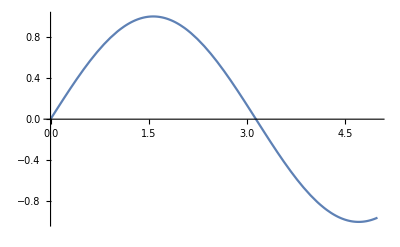

Full input to Wolfram Alfpha

where is the ISS

WolframAlphaQueryResults

Cell types:  working, slideshow,printout.  they depend on stylesheet. this can be modified in format - style

Cell Grouping
Cell show expression shows all the code for each cell

Cell properties - 
Cell tags NotebookLocate
Forms

```mathematica
?System *Form
```

Information::notfound: Symbol System not found.

```mathematica
mat = MatrixForm[{{1,2},{3,4}}]
```

(1 | 2
3 | 4)

```mathematica
Det[mat]
```

Det[(1 | 2
3 | 4)]

didn’t work because any Form command introduces formatting for output, not for input

```mathematica
Det[{{1,2},{3,4}}]
```

-2

```mathematica
{{1,2},{3,4}}//MatrixForm
```

(1 | 2
3 | 4)